```mathematica
makeLine[x_, y_, L_, theta_]:={{x, y}, {x+L*Cos[theta], y+L*Sin[theta]}}
```

```mathematica
calculateRange[{{xa1_, ya1_}, {xa2_, ya2_}}]:=Module[{A, B},
A=Min[{xa1, xa2}];
B=Max[{xa1, xa2}];
{A,B}]
```

```mathematica
makeLine[x_, y_, L_, theta_]:={{x, y}, {x+L*Cos[theta], y+L*Sin[theta]}}
```

```mathematica
getSlope[{{xa1_, ya1_}, {xa2_, ya2_}}]:=If[xa2-xa1== 0, "undefined",(ya2-ya1)/(xa2-xa1)]
```

```mathematica
getYintercept[{{xa1_, ya1_}, {xa2_, ya2_}}]:=Module[{m},
m=getSlope[ {{xa1, ya1}, {xa2, ya2}}];
 If[m=="undefined", "undefined", ya1-m*xa1] ]
```

```mathematica
getInfo[line_]:=Module[{A, B, m, b},
{A, B}=calculateRange[line];
m=getSlope[line];
b=getYintercept[line];
{m, b, A, B}]
```

```mathematica
findXvalues[line0_, lineN_]:=Module[{x0, xN},
(* Gets the x value of the Original line with the higher y value *)
x0=Sort[line0, #1[[2]]>#2[[2]] &][[1]][[1]];
(* Gets the x value of the new line with the lower y value *)
xN=Sort[lineN, #1[[2]]<#2[[2]] &][[1]][[1]];
{x0, xN}]
```

```mathematica
determineNewSettleO1[line0_, lineN_]:=Module[{m0, b0, A0, B0, mN, bN, AN, BN, bNN},
{m0, b0, A0, B0}=getInfo[line0];
{mN, bN, AN, BN}=getInfo[lineN];
bNN=If[AN≤A0 && A0<BN,
Max[{A0*(m0-mN)+b0, BN*(m0-mN)+b0}],
Max[{AN*(m0-mN)+b0, B0*(m0-mN)+b0}]];
{{AN, mN*AN+bNN}, {BN, mN*BN+bNN}}]
```

```mathematica
computeSettle[line_, collection_]:=Module[{m, b, A, B, bNN},
{m, b, A, B}=getInfo[line];
bNN=Max[Select[determineNewSettle[#, line]&/@collection, #≠"none"&]];
{{A, m*A+bNN}, {B, m*B+bNN}}
]
```

```mathematica
determineNewSettleO2[line0_, lineN_]:=Module[{m0, b0, A0, B0, mN, bN, AN, BN, x0, xN, b1, b2, bNN},
{m0, b0, A0, B0}=getInfo[line0];
{mN, bN, AN, BN}=getInfo[lineN];
{x0, xN}=findXvalues[line0, lineN];
(* Both of the following can be true *)
b1=If[AN≤ x0 && x0 ≤ BN, 
x0*(m0-mN)+b0, "none"];
b2 =If[A0≤ xN && xN ≤ B0,
xN*(m0-mN)+b0, "none"];
bNN=Select[{b1, b2}, #≠ "none" &][[1]];
{{AN, mN*AN+bNN}, {BN, mN*BN+bNN}}]
```

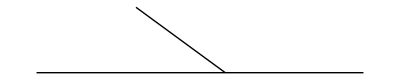

```mathematica
determineNewSettle[line0_, lineN_]:=Module[{m0, b0, A0, B0, mN, bN, AN, BN, x0, xN, b1, b2, b3, b4, bNN},
{m0, b0, A0, B0}=getInfo[line0];
{mN, bN, AN, BN}=getInfo[lineN];
b1=If[AN≤ A0 && A0 ≤ BN, 
A0*(m0-mN)+b0, "none"];
b2=If[AN≤ B0 && B0 ≤ BN, 
B0*(m0-mN)+b0, "none"];
b3=If[A0≤ AN && AN ≤ B0, 
AN*(m0-mN)+b0, "none"];
b4=If[A0≤ BN && BN ≤ B0, 
BN*(m0-mN)+b0, "none"];
bNN=Max[Select[{b1, b2, b3, b4}, #≠"none" &]];
(* If[bNN>-Infinity, 
{{AN, mN*AN+bNN}, {BN, mN*BN+bNN}}, "none"]*)
If[bNN> -Infinity, bNN, "none"]]
```

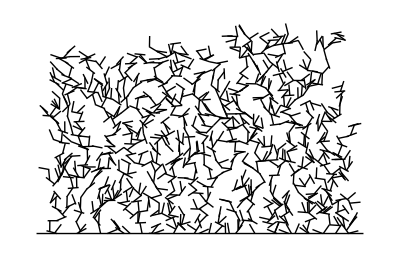

```mathematica
width=30;
bottom={{0,0}, {width, 0}};
collection={bottom};
l=makeLine[1+(width-2)*Random[],  0, 1,Pi*Random[]];
collection=Append[collection, l];
For[i=1, i<1000, i++,
l=makeLine[1+(width-2)Random[],  0, 1,Pi*Random[]];
ans=computeSettle[l, collection];
collection=Append[collection, ans];
]
Graphics[{Line[#]&/@collection}]
```